```mathematica
Gdot[G_]:=a-b G- G/(1+G^2)
```

```mathematica
Gdot'[G]
```

-b+(2 G^2)/((1+G^2)^2)-1/(1+G^2)

```mathematica
ToExpression["\\dot{G}",TeXForm]
```

Ġ

```mathematica
(ⅆ Ġ)/ⅆG
```

(ⅆ Ġ)/ⅆG

```mathematica
b=0.12
```

0.12

```mathematica
a=√3(b+1/4)
```

0.640859

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Show[Plot[Gdot[G],{G,1,2.5},AxesLabel->{"G","Ġ"}],ParametricPlot[{√3,t},{t,-0.01,0.01},PlotStyle->{Red,Dashed}]]
```

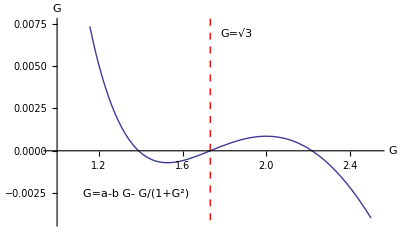

```mathematica
Show[Plot[Gdot'[G],{G,1,2.5},AxesLabel->{"G","ⅆĠ/ⅆG"}],ParametricPlot[{√3,t},{t,-0.09,0.01},PlotStyle->{Red,Dashed}]]
```